```mathematica
SetDirectory[NotebookDirectory[]];

Bx0[x_,y_,z_]:=NIntegrate[
(R z Cos[φ])/((x^2+y^2+z^2+R^2-2x R Cos[φ]-2y R Sin[φ])^(3/2)),
{φ,0,2π},MaxRecursion->12];
By0[x_,y_,z_]:=NIntegrate[
(R z Sin[φ])/((x^2+y^2+z^2+R^2-2x R Cos[φ]-2y R Sin[φ])^(3/2)),
{φ,0,2π},MaxRecursion->12];
Bz0[x_,y_,z_]:=NIntegrate[
(R (R-x Cos[φ]-y Sin[φ]))/((x^2+y^2+z^2+R^2-2x R Cos[φ]-2y R Sin[φ])^(3/2)),
{φ,0,2π},MaxRecursion->12];
Bx[x_,y_,z_]:=Bx0[x,y,z-d/2]+Bx0[x,y,z+d/2];
By[x_,y_,z_]:=By0[x,y,z-d/2]+By0[x,y,z+d/2];
Bz[x_,y_,z_]:=Bz0[x,y,z-d/2]+Bz0[x,y,z+d/2];
R=1.0;d=2 R;n=50;
data1={};
Do[
Do[
Do[AppendTo[data1,{(3R)/n i,(3R)/n j,(2d)/n k,
Bx[(3R)/n i,(3R)/n j,(2d)/n k]}],
{i,-n/2,n/2}],
{j,-n/2,n/2}],
{k,-n/2,n/2}]
Bx=Interpolation[data1];
Bx>>"Bx50";
data2={};
Do[
Do[
Do[AppendTo[data2,{(3R)/n i,(3R)/n j,(2d)/n k,
By[(3R)/n i,(3R)/n j,(2d)/n k]}],
{i,-n/2,n/2}],
{j,-n/2,n/2}],
{k,-n/2,n/2}]
By=Interpolation[data2];
By>>"By50";
data3={};
Do[
Do[
Do[AppendTo[data3,{(3R)/n i,(3R)/n j,(2d)/n k,
Bz[(3R)/n i,(3R)/n j,(2d)/n k]}],
{i,-n/2,n/2}],
{j,-n/2,n/2}],
{k,-n/2,n/2}]
Bz=Interpolation[data3];
Bz>>"Bz50";
```

```mathematica
SetDirectory[NotebookDirectory[]];
R=1;d=2 R;
sc=1.75851×10^11×0.35×10^-5;time=60 10^-6;
<<"Bx50";
Bx=%;
<<"By50";
By=%;
<<"Bz50";
Bz=%;
equ={x''[t]==-sc (y'[t] Bz[x[t],y[t],z[t]]-
z'[t] By[x[t],y[t],z[t]]),
y''[t]==-sc (z'[t] Bx[x[t],y[t],z[t]]-
x'[t] Bz[x[t],y[t],z[t]]),
z''[t]==-sc (x'[t] By[x[t],y[t],z[t]]-
y'[t] Bx[x[t],y[t],z[t]]),
x[0]==0,x'[0]==0,y[0]==0,y'[0]==0.3 10^6,
z[0]==0,z'[0]==0.15 10^6};
s=NDSolve[equ,{x,y,z},{t,0,time}]
{x,y,z}={x,y,z}/.s[[1]];
Manipulate[ParametricPlot3D[{x[t],y[t],z[t]},
{t,0,t0},Ticks->None,AxesStyle->Thin,Axes->True,
AxesLabel->{"x","y","z"}, 
PlotStyle->{Thin,Black},AspectRatio->2,PlotRange->{{- 0.3 d,0.3 d},{-0.3 d,0.3 d},{-0.75 d,0.75 d}}],{t0,0.001 time,time}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {0.0000241858}. NIntegrate obtained -3.81639×10^-17 and 4.32444×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {0.0000241858}. NIntegrate obtained 3.81639×10^-17 and 4.32444×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {0.0000241858}. NIntegrate obtained -3.81639×10^-17 and 4.32444×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

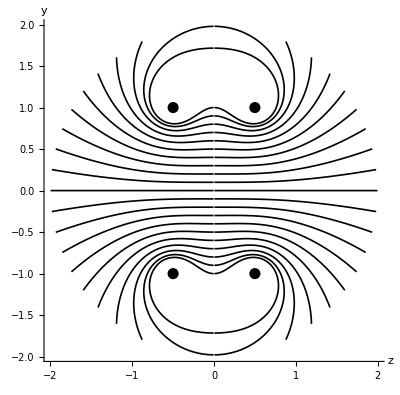

```mathematica
By0[y_,z_]:=
NIntegrate[(R z Sin[φ])/((z^2+y^2+R^2-2R y Sin[φ])^(3/2)),{φ,0,2π}];
Bz0[y_,z_]:=
NIntegrate[(R (R-y Sin[φ]))/((z^2+y^2+R^2-2R y Sin[φ])^(3/2)),{φ,0,2π}];
By[y_,z_]:=By0[y,z-d/2]+By0[y,z+d/2];
Bz[y_,z_]:=Bz0[y,z-d/2]+Bz0[y,z+d/2];
d=R=1;r1=0.005R;r2=2R;forceline={};step=0.005 R;
Do[
θ=0;p={r1,y0};single={};
While[(Abs[p[[1]]]>=r1)∧(Norm[p]<r2),
AppendTo[single,p];p=p+(Bz[p[[2]],p[[1]]]^2+By[p[[2]],p[[1]]]^2)^0.5/(Bz[0,0]^2+By[0,0]^2)^0.5*step {Cos[θ],Sin[θ]};
θ=Arg[Bz[p[[2]],p[[1]]]+ⅈ By[p[[2]],p[[1]]]]];
AppendTo[forceline,single];
m=Length[single];
single=Table[{-single[[j,1]],single[[j,2]]},{j,m}];
AppendTo[forceline,single],
{y0,-R,R,0.1R}]
Show[Graphics[{Thickness[0.003],Line/@forceline}],
Axes->True,AxesLabel->{"z","y"},AspectRatio->Automatic,
Epilog->{PointSize[0.02],
Point/@{{d/2,-R},{d/2,R},{-d/2,R},{-d/2,-R}}}]
```